```mathematica
sol=DSolve[{(x-1)*y''[x]-x*y'[x]+y[x]==-(1-x)^2,y[0]==0,y[2]+1/2 y'[2]==-1/4},y,{x,0,2}]
```

{{y→Function[{x},1-ⅇ^x-(29 x)/10+(3 ⅇ^2 x)/5+x^2]}}

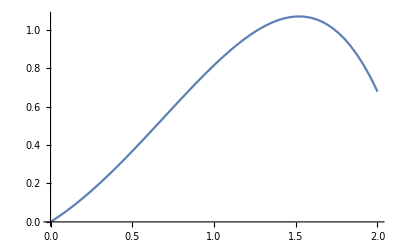

```mathematica
Plot[First[y[x]/.sol],{x,0,2}]
```